```mathematica
Nt = 15;
ti = 0; tf = 2*Pi; 
deltat = (tf - ti) /Nt ;
Nx = 15; 
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax)
k = .;
j  = .;
```

1

```mathematica
(*T = Table[tn = ti + n *deltat, {n, 0, Nt  }]//N;
X =  Table[xm = xi + m *deltax, {m, 0, Nx }]//N*)

h = (2π) / Nx;

T = Array[#&,Nt,{ti,tf}]//N;
(*X = Array[#&,Nx,{xi,xf}]//N;*)

(*X spacing as defined in http://easymeca.mobile.basilisk.fr/sandbox/easystab/matlabdifmatsuite.pdf*)
X = Table[(i-1)*h,{i,1,Nx}]//N;

D1 = Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}]//N;
D1//MatrixForm
```

(0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487
-2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293
1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651
-0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816
0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735
-0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731
0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754
-0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754
0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731
-0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735
0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651 | -0.672816
-0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293 | 0.850651
0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487 | -1.2293
-1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0. | 2.40487
2.40487 | -1.2293 | 0.850651 | -0.672816 | 0.57735 | -0.525731 | 0.502754 | -0.502754 | 0.525731 | -0.57735 | 0.672816 | -0.850651 | 1.2293 | -2.40487 | 0.)

```mathematica
f[x_] = Exp[-16* x^2]
```

ⅇ^(-16 x^2)

```mathematica
F = f[X]
```

{1.,0.0603645,0.0000132778,1.06423×10^-11,3.10817×10^-20,3.3078×10^-31,1.28274×10^-44,1.81258×10^-60,9.33301×10^-79,1.75109×10^-99,1.19718×10^-122,2.98244×10^-148,2.70738×10^-176,8.95547×10^-207,1.07942×10^-239}

```mathematica
F' = f'[X]
```

{0.,-0.809133,-0.000355955,-4.27951×10^-10,-1.66649×10^-18,-2.21691×10^-29,-1.03164×10^-42,-1.70073×10^-58,-1.00081×10^-76,-2.11247×10^-97,-1.60471×10^-120,-4.39748×10^-146,-4.3548×10^-174,-1.56052×10^-204,-2.02562×10^-237}

```mathematica
D1.F
```

{0.145152,-2.40484,1.08413,-0.776477,0.621484,-0.536747,0.490889,-0.471026,0.472413,-0.495389,0.545621,-0.637972,0.810044,-1.17796,2.33067}

```mathematica
Abs[D1.F - f'[X]]
```

{0.145152,1.5957,1.08448,0.776477,0.621484,0.536747,0.490889,0.471026,0.472413,0.495389,0.545621,0.637972,0.810044,1.17796,2.33067}

```mathematica
Max[Abs[D1.F - f'[X]]]
```

2.33067

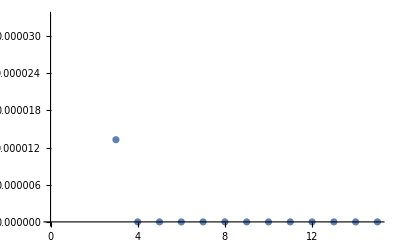

```mathematica
ListPlot[f[X]]
```

```mathematica
(*CN*)
I1 = Length[D1];
A = I1 - ((deltat / 2) * D1);
B = I1 + ((deltat / 2) * D1);
M = Inverse[A].B;
```

```mathematica
(*Euler*)
```

```mathematica
Ieuler = IdentityMatrix[Length[D1]];

euler = Ieuler + deltat*D1;
```

```mathematica
(*Eigenvalues*)
```

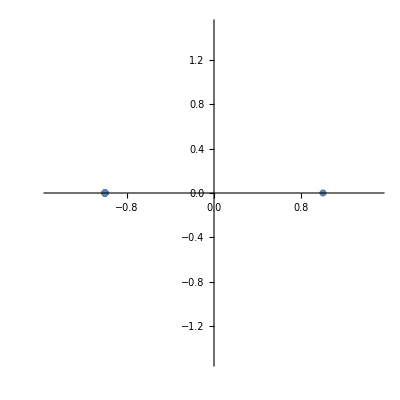

```mathematica
(*CN*)
evals = Eigenvalues[N[M]];
realEvals = Re[evals];
imagEvals = Im[evals];
Abs[evals];
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

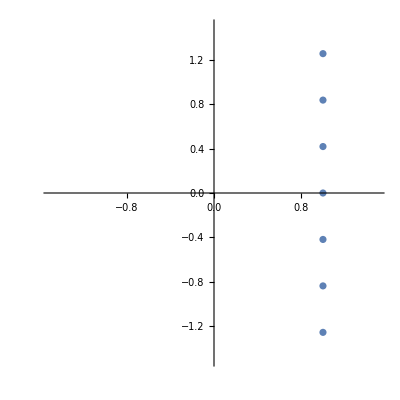

```mathematica
(*Euler*)
evalsEuler = Eigenvalues[N[euler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];
ListPlot[{Transpose[{realEvalsEuler,imagEvalsEuler}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```